```mathematica
(*** Bottleneck experiment ***)
```

```mathematica
(*** from part1-binomial.nb , we have for the general BID generating function and binomial cell divisions ***)
```

```mathematica
gtmp=((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) ((l^n lp (-1+z) (λ+(-2+l) ν)+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν))/((-1+l) l^n lp (-1+z) λ+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν)))^m0 (((ⅇ^((λ-ν) τ) lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(2 (-1+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),1/2 ⅇ^((λ-ν) τ),1+n])/((lp (-1+z) λ+l (-z λ+ν)) QPochhammer[((ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),1/2 ⅇ^((λ-ν) τ),1+n]))^(α/λ)
```

((-λ+ν)/(ⅇ^(t (λ-ν)) (-1+z) λ-z λ+ν))^(α/λ) ((l^n lp (-1+z) (λ+(-2+l) ν)+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν))/((-1+l) l^n lp (-1+z) λ+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν)))^m0 (((ⅇ^((λ-ν) τ) lp (-1+z) λ+l (-z λ+ν)) QPochhammer[(2 (-1+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),1/2 ⅇ^((λ-ν) τ),1+n])/((lp (-1+z) λ+l (-z λ+ν)) QPochhammer[((ⅇ^((λ-ν) τ) (-2+l)+l) lp (-1+z) λ)/(l (lp (-1+z) λ+(-2+l) (z λ-ν))),1/2 ⅇ^((λ-ν) τ),1+n]))^(α/λ)

```mathematica
(*** to remove immigration we can straightforwardly set α = 0 ***)
```

```mathematica
FullSimplify[gtmp/.α->0]
```

((l^n lp (-1+z) (λ+(-2+l) ν)+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν))/((-1+l) l^n lp (-1+z) λ+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν)))^m0

```mathematica
(*** decompose this into numerator and denominator to allow recursion over different dynamics phases ***)
```

```mathematica
o1num = l^n lp (-1+z) (λ+(-2+l) ν)+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν);
o1denom =(-1+l) l^n lp (-1+z) λ+2^n ((lp-(-2+l+lp) z) λ+(-2+l) ν);
```

```mathematica
AB = FullSimplify[Coefficient[o1num, z]]
BB = FullSimplify[o1num - z Coefficient[o1num, z]]
CB = FullSimplify[Coefficient[o1denom, z]]
DB = FullSimplify[o1denom- z Coefficient[o1denom, z]]
```

-2^n (-2+l+lp) λ+l^n lp (λ+(-2+l) ν)

-l^n lp (λ+(-2+l) ν)+2^n (lp λ+(-2+l) ν)

(-1+l) l^n lp λ-2^n (-2+l+lp) λ

(2^n-(-1+l) l^n) lp λ+2^n (-2+l) ν

```mathematica
coeffs = {AB, BB, CB, DB};
```

```mathematica
(*** now label each set of parameters differently for each phase. here we consider 4 phases but will only end up using 2. ***)
```

```mathematica
c1 =Simplify[coeffs/.lp->lp1/.l->l1/.λ->λ1/.ν->ν1/.n->n1]
c2=Simplify[coeffs/.lp->lp2/.l->l2/.λ->λ2/.ν->ν2/.n->n2]
c3 =Simplify[coeffs/.lp->lp3/.l->l3/.λ->λ3/.ν->ν3/.n->n3]
c4 =Simplify[coeffs/.lp->lp4/.l->l4/.λ->λ4/.ν->ν4/.n->n4]
```

{-2^n1 (-2+l1+lp1) λ1+l1^n1 lp1 (λ1+(-2+l1) ν1),-l1^n1 lp1 (λ1+(-2+l1) ν1)+2^n1 (lp1 λ1+(-2+l1) ν1),(-1+l1) l1^n1 lp1 λ1-2^n1 (-2+l1+lp1) λ1,(2^n1-(-1+l1) l1^n1) lp1 λ1+2^n1 (-2+l1) ν1}

{-2^n2 (-2+l2+lp2) λ2+l2^n2 lp2 (λ2+(-2+l2) ν2),-l2^n2 lp2 (λ2+(-2+l2) ν2)+2^n2 (lp2 λ2+(-2+l2) ν2),(-1+l2) l2^n2 lp2 λ2-2^n2 (-2+l2+lp2) λ2,(2^n2-(-1+l2) l2^n2) lp2 λ2+2^n2 (-2+l2) ν2}

{-2^n3 (-2+l3+lp3) λ3+l3^n3 lp3 (λ3+(-2+l3) ν3),-l3^n3 lp3 (λ3+(-2+l3) ν3)+2^n3 (lp3 λ3+(-2+l3) ν3),(-1+l3) l3^n3 lp3 λ3-2^n3 (-2+l3+lp3) λ3,(2^n3-(-1+l3) l3^n3) lp3 λ3+2^n3 (-2+l3) ν3}

{-2^n4 (-2+l4+lp4) λ4+l4^n4 lp4 (λ4+(-2+l4) ν4),-l4^n4 lp4 (λ4+(-2+l4) ν4)+2^n4 (lp4 λ4+(-2+l4) ν4),(-1+l4) l4^n4 lp4 λ4-2^n4 (-2+l4+lp4) λ4,(2^n4-(-1+l4) l4^n4) lp4 λ4+2^n4 (-2+l4) ν4}

```mathematica
(*** recursive expression for the overall generating function, as in the text ***)
```

```mathematica
g2 = Simplify[(c2[[1]] z + c2[[2]])/(c2[[3]] z+ c2[[4]])];
g1 = Simplify[(c1[[1]] g2 + c1[[2]])/(c1[[3]] g2 + c1[[4]])];
goverall2 = g1^m0;
```

```mathematica
Goverall = goverall2;
```

```mathematica
(*** we can now get statistics of the overall system ***)
```

```mathematica
mean4 = Simplify[D[Goverall,z]/.z->1]
```

2^(-n1-n2) l1^n1 l2^n2 lp1 lp2 m0

```mathematica
var4 =Simplify[(D[Goverall, {z, 2}] +D[Goverall, z] - (D[Goverall, z])^2)/.z->1];
```

```mathematica
(*** use some parameters to compare to stochastic simulation ***)
```

```mathematica
X1=12;
nmax = 240;
```

```mathematica
rep = 0.0693147;
```

```mathematica
sm0 = 100000;
```

```mathematica
Lsubs = {lp1->If[nt<X1,Exp[(λ1-ν1) t],1], lp2->If[nt≥ X1, Exp[(λ2-ν2)t], 1],l1->Exp[(λ1-ν1) τ], l2->Exp[(λ2-ν2)τ]};
subs1 = {ν1 -> 0, ν2->0, λ1->rep, λ2->rep, τ->10, m0->sm0};
subs2 = {ν1 -> 0, ν2->0, λ1->0.02,λ2->(2 rep-0.02), τ->10, m0->sm0};
subs3 = {ν1 -> 0, ν2->0, λ1->0.03,λ2->(2rep-0.03),τ->10, m0->sm0};
subs4 = {ν1 -> 0, ν2->0, λ1->0.04, λ2->(2rep-0.04), τ->10, m0->sm0};
subs5= {ν1 -> 0, ν2->0, λ1->0.05, λ2->(2 rep - 0.05), τ->10, m0->sm0};

nsubs = {n1->If[nt<X1, nt,X1], n2->If[nt≥ X1, nt-X1, 0], t->Mod[nn, 10]+1};
n1subs = {nt->Floor[nn/10]};
```

```mathematica
(*** all this does is produce numerical tables of results for the different parameterisations we use ***)
```

```mathematica
mean1the = Table[{nn,(mean4/.Lsubs/.subs1/.nsubs/.n1subs)}, {nn, 0, nmax}];
var1the = Table[{nn,(var4/.Lsubs/.subs1/.nsubs/.n1subs)}, {nn, 0,nmax}];
cv1the = Table[{mean1the[[nn]][[1]], Sqrt[var1the[[nn]][[2]]]/mean1the[[nn]][[2]]}, {nn, 1, nmax}];
mean2the = Table[{nn,(mean4/.Lsubs/.subs2/.nsubs/.n1subs)}, {nn, 0, nmax}];
var2the = Table[{nn,(var4/.Lsubs/.subs2/.nsubs/.n1subs)}, {nn, 0, nmax}];
cv2the = Table[{mean2the[[nn]][[1]], Sqrt[var2the[[nn]][[2]]]/mean2the[[nn]][[2]]}, {nn, 1, nmax}];
mean3the = Table[{nn,(mean4/.Lsubs/.subs3/.nsubs/.n1subs)}, {nn, 0,nmax}];
var3the = Table[{nn,(var4/.Lsubs/.subs3/.nsubs/.n1subs)}, {nn, 0, nmax}];
cv3the = Table[{mean3the[[nn]][[1]], Sqrt[var3the[[nn]][[2]]]/mean3the[[nn]][[2]]}, {nn, 1, nmax}];
mean4the = Table[{nn,(mean4/.Lsubs/.subs4/.nsubs/.n1subs)}, {nn, 0, nmax}];
var4the = Table[{nn,(var4/.Lsubs/.subs4/.nsubs/.n1subs)}, {nn, 0, nmax}];
cv4the = Table[{mean4the[[nn]][[1]], Sqrt[var4the[[nn]][[2]]]/mean4the[[nn]][[2]]}, {nn, 1, nmax}];
mean5the = Table[{nn,(mean4/.Lsubs/.subs5/.nsubs/.n1subs)}, {nn, 0, nmax}];
var5the = Table[{nn,(var4/.Lsubs/.subs5/.nsubs/.n1subs)}, {nn, 0, nmax}];
cv5the = Table[{mean4the[[nn]][[1]], Sqrt[var4the[[nn]][[2]]]/mean4the[[nn]][[2]]}, {nn, 1, nmax}];
```

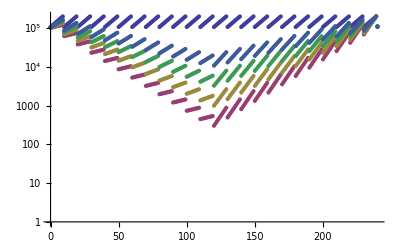

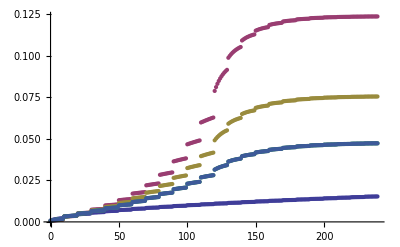

```mathematica
ListLogPlot[{mean1the, mean2the,mean3the, mean4the, mean5the}]
ListPlot[{cv1the, cv2the,cv3the, cv4the, cv5the}]
```

```mathematica
(*** output results to files ***)
```

```mathematica
etab = Table[{mean1the[[i]][[1]], mean1the[[i]][[2]],var1the[[i]][[2]]}, {i , 1, Length[mean1the]-1}];
Export["bneckanala.dat", etab];
etab = Table[{mean2the[[i]][[1]], mean2the[[i]][[2]], var2the[[i]][[2]]}, {i , 1, Length[mean2the]-1}];
Export["bneckanalb.dat", etab];
etab = Table[{mean3the[[i]][[1]], mean3the[[i]][[2]], var3the[[i]][[2]]}, {i , 1, Length[mean3the]-1}];
Export["bneckanalc.dat", etab];
etab = Table[{mean4the[[i]][[1]], mean4the[[i]][[2]], var4the[[i]][[2]]}, {i , 1, Length[mean4the]-1}];
Export["bneckanald.dat", etab];
etab = Table[{mean5the[[i]][[1]], mean5the[[i]][[2]], var5the[[i]][[2]]}, {i , 1, Length[mean5the]-1}];
Export["bneckanale.dat", etab];
```

```mathematica
var=FullSimplify[var4/.t->0/.lp1->1/.lp2->1/.l1->Exp[λ1 τ]/.l2 ->Exp[λ2 τ]/.ν1->0/.ν2->0/.λ2->(2ρ-λ1)/.n2->n1/.ρ->Log[2]/τ, Assumptions->{λ1 >0, λ2>0, n1 >0, n2>0, τ>0, ρ>0}]
```

(ⅇ^(-n1 λ1 τ) (2+ⅇ^(λ1 τ)) (-2^n1+ⅇ^(n1 λ1 τ)) m0)/(-2+ⅇ^(λ1 τ))

```mathematica
FullSimplify[mean4/.lp1->1/.lp2->1/.l2->1/.l1->Exp[λ1 τ]/.n2->0, Assumptions->{λ1 >0, λ2>0, n1 >0, n2>0, τ>0, ρ>0}]
```

2^-n1 ⅇ^(n1 λ1 τ) m0

```mathematica
bnsoln=Solve[bneck == 2^-n1 ⅇ^(n1 λ1 τ) m0, λ1]/.C[1]->0
```

{{λ1→Log[(2^n1 bneck)/m0]/(n1 τ)}}

```mathematica
varbn=FullSimplify[var/.bnsoln[[1]], Assumptions->{λ1 >0, λ2>0, n1 >0, n2>0, τ>0, ρ>0, bneck>0}]
```

((1+(bneck/m0)^(1/n1)) (bneck-m0) m0)/(bneck (-1+(bneck/m0)^(1/n1)))